# CS 274A Homework 5

## Mixture Model

Baoxiang Pan  63324929

## Algorithm 1: K-means Clustering

### Algorithm Description The K-means algorithm was implemented with Mathematica codes as follows:

```mathematica
KMeans[k_,data_]:=
Module[{Renew,Label,Iteration},
clusters=RandomSample[data,k];
Label[clusters_]:=Flatten[Table[Ordering[Table[EuclideanDistance[data[[i]],clusters[[j]]],{j,Length[clusters]}],1],{i,Length[data]}]];
Renew[labels_]:=
Module[{position},
position=PositionIndex[labels];
Return[Table[Mean[data[[position[[i]]]]],{i,Length[position]}]]];
Iteration[labels_,clusters_]:=
Module[{newlabels,newclusters},
newclusters=Renew[labels];
newlabels=Label[newclusters];
If[newlabels==labels,labels,Iteration[newlabels,newclusters]]];
Return[Iteration[clusters,Label[clusters]]]]
```

### To start with different cluster centers and keep best performace, the codes are as follows:

```mathematica
InitialTryKMeans[k_, data_, labels_, times_] := 
Module[{best, Try}, 
best = KMeans[k, data]; 
Try[t_] := If[t == 0, best, Module[{new}, new = KMeans[k, data]; If[EuclideanDistance[new, labels] < EuclideanDistance[best, labels], 
best = new; Try[t - 1], Try[t - 1]]]]; 
Return[Try[times]]]
```

### Results

```mathematica
SetDirectory["/Users/penn/Documents/Code/Github/My_Lib/Mathematica_Lib/Machine Learning/H5"];
```

#### Dataset I

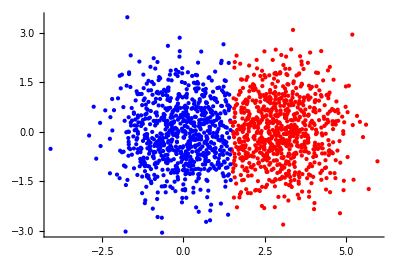

```mathematica
data=Import["dataset1","Table"];
rdata=RandomSample[data];
z=KMeans[2,rdata];
Show[Table[If[z[[i]]==1,Graphics[{Red,Point[rdata[[i]]]}],Graphics[{Blue,Point[rdata[[i]]]}]],{i,1,Length[z]}],Axes->True]
```

```mathematica
Dataset II
```

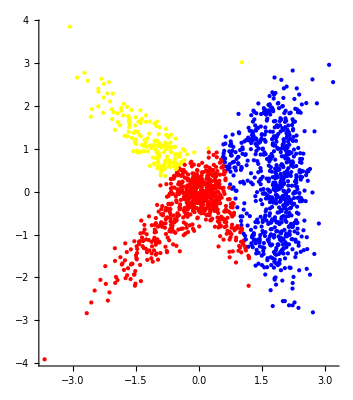

```mathematica
data=Import["dataset2","Table"];
rdata=RandomSample[data];
z=KMeans[3,rdata];
Show[Table[If[z[[i]]==1,Graphics[{Red,Point[rdata[[i]]]}],If[z[[i]]==2,Graphics[{Blue,Point[rdata[[i]]]}],Graphics[{Yellow,Point[rdata[[i]]]}]]],{i,1,Length[z]}],Axes->True]
```

```mathematica
Dataset III
```

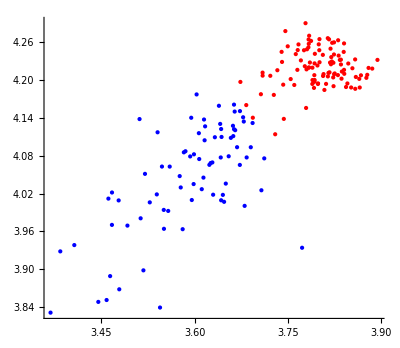

```mathematica
data=Import["dataset3","Table"];
rdata=RandomSample[data];
z=KMeans[2,rdata];
Show[Table[If[z[[i]]==1,Graphics[{Red,Point[rdata[[i]]]}],Graphics[{Blue,Point[rdata[[i]]]}]],{i,1,Length[z]}],Axes->True]
```

#### Dataset IV

```mathematica
pic=Import["clown.jpg"];
data=Flatten[Table[PixelValue[pic,{i,j}],{i,ImageDimensions[pic][[1]]},{j,ImageDimensions[pic][[2]]}],1];
rdata=RandomSample[data];
z=KMeans[4,rdata];
Show[Table[If[z[[i]]==1,Graphics3D[{Red,Point[rdata[[i]]]}],If[z[[i]]==2,Graphics3D[{Blue,Point[rdata[[i]]]}],If[z[[i]]==3,Graphics3D[{Yellow,Point[rdata[[i]]]}],Graphics3D[{Green,Point[rdata[[i]]]}]]]],{i,1,Length[z]}],Axes->True]
```

-Graphics3D-

## Algorithm II: EM Algorithm

### Algorithm Description

```mathematica
EMGaussian[data_,k_]:=
Module[{n,d,WeightInitialization,ParameterGeneration, MatrixCal,MatrixEvolution,Loglikelihood,matrixlists,loglists},
n = Dimensions[data][[1]];
d = Dimensions[data][[2]];

WeightInitialization =
  Module[{a},
   Table[
    a = RandomVariate[DirichletDistribution[ConstantArray[k, k]]];
    Append[a, 1 - Total[a]],
    {i , n}]];

ParameterGeneration[weight_] :=
  Module[{nn, alpha, mu, SCal, sigma},
   nn = Total[weight, {1}];
   alpha = nn/Dimensions[weight][[1]];
   mu = Table[(Transpose[data].weight)[[i]]/nn, {i, 
      Dimensions[data][[2]]}];
   SCal[q_] :=
    Module[{F, x},
     F[lis_] := 
      Flatten[ArrayReshape[lis, {Length[lis], 1}].ArrayReshape[
         lis, {1, Length[lis]}]];
     x = Map[F, Table[data[[j]] - mu[[All, q]], {j, n}]];
     Return[weight[[All, q]].x/nn[[q]]]];
   sigma = Transpose[Table[SCal[i], {i, Length[nn]}]];
   Return[{alpha, mu, sigma}]];

MatrixCal[weights_]:=
Module[{alpha, sigma, mu, matrix},
   {alpha, mu, sigma} = ParameterGeneration[weights];
   matrix = 
    Table[PDF[
       MultinormalDistribution[mu[[All, j]], 
        ArrayReshape[sigma[[All, j]], {d, d}]], data[[i]]]*
      alpha[[j]], {i, n}, {j, k}];
	Return[matrix]];

MatrixEvolution[matrix_] :=MatrixCal[Table[matrix[[i]]/Total[matrix[[i]]], {i, n}]];

Loglikelihood[matrix_]:=Total[Table[Log[Total[matrix[[i]]]],{i,n}]];

matrixlists=NestList[MatrixEvolution,MatrixCal[WeightInitialization],100];
loglists=Map[Loglikelihood,matrixlists];

Return[{matrixlists,loglists}]]
```

### Results

#### Dataset I

```mathematica
data=Import["dataset1","Table"];
rdata=RandomSample[data];
{matrix,loglists}=EMGaussian[rdata,2];
final=Last[matrix];
Show[Table[If[final[[i]][[1]]>final[[i]][[2]],Graphics[{Red,Point[rdata[[i]]]}],Graphics[{Blue,Point[rdata[[i]]]}]],{i,1,Length[final]}],Axes->True]
```

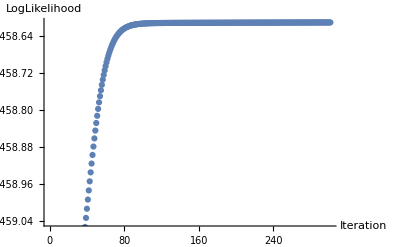

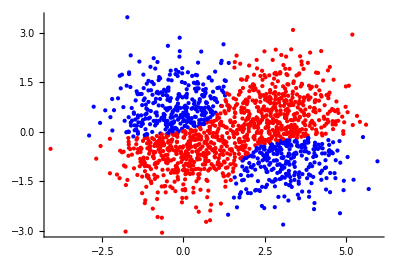

#### Dataset II

```mathematica
data=Import["dataset2","\"""Table""\""];
rdata=RandomSample[data];
{matrix,loglists}=EMGaussian[rdata,3];
final=Last[matrix];
Show[Table[If[And[final[[i]][[1]]>final[[i]][[2]],final[[i]][[1]]>final[[i]][[3]]],Graphics[{Red,Point[rdata[[i]]]}],
				If[And[final[[i]][[2]]>final[[i]][[1]],final[[i]][[2]]>final[[i]][[3]]],Graphics[{Blue,Point[rdata[[i]]]}],Graphics[{Yellow,Point[rdata[[i]]]}]]],{i,1,Length[final]}],Axes->True]
```

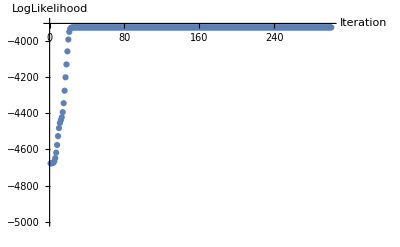

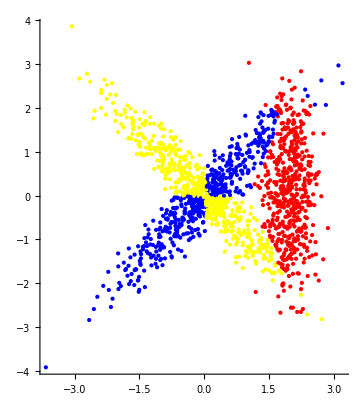

#### Dataset III

```mathematica
data=Import["dataset3","Table"];
rdata=RandomSample[data];
{matrix,loglists}=EMGaussian[rdata,2];
final=Last[matrix];
Show[Table[If[final[[i]][[1]]>final[[i]][[2]],Graphics[{Red,Point[rdata[[i]]]}],Graphics[{Blue,Point[rdata[[i]]]}]],{i,1,Length[final]}],Axes->True]
```